# CARBAPENEM RESISTANCE MODEL

## Data

### Preparing Directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];
```

### Load Data

Reading country data on consumption and resistance and assigning them to appropriate variables.

```mathematica
countryname="US_DDD"; 
data=Import["DataSheet_cddep.xlsx",{"Data",countryname}];
data = data[[All,2;;]];
years = data[[1]];
tt = Length[years]; 
nop = (Length[data]-5)/2; (*# of pathogens*)
isolates = data[[2;;Length[data]-4;;2]];
resistance = data[[3;;Length[data]-4;;2]];
rfreq =resistance/isolates;
cbpcon =  data[[-1]]; (*CBP consumption data*)
cbpp = data[[-3,1;;nop]]; (*CBP consumption for pathogens: KP, PA, AB, EA/C*)
cbppneu = cbpcon*data[[-2,1]]; (*CBP consumption for pneumonia*)
cbp =data[[-2,1]]*Table[cbpcon*cbpp[[i]],{i,1,nop}];
```

## Model

### Parameters & Model Structure

r(t) = frequency of resistance
k_s= natural growth rate of the sensitive strain
k_r= natural growth rate of the resistance strain (k_r < k_s)
θ = k_r-k_s< 0 
a = CBP consumption (DDD)

```mathematica
r[t_,r0_,ks_,θ_]:=ⅇ^(Total[ks*a[[1;;t]]]+θ*t)/((1/r0)-1+ⅇ^(Total[ks*a[[1;;t]]]+ θ*t));
```

### Likelihood

```mathematica
Lik[r0_,ks_,θ_]:= Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,θ]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,θ]],{j,1,tt}]]
```

### Model Fitting

```mathematica
max  = PadRight[{},nop,Null];
fr0 = max; fks=max; fθ=max;
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],{max[[i]],{fr0[[i]],fks[[i]],fθ[[i]]}}=NMaximize[{Lik[r0,ks,θ],0<r0<1,θ<-0.1},{r0,ks,θ}, MaxIterations->100000]}]

fr0 = Table[fr0[[i]][[2]],{i,1,nop}];
fks = Table[fks[[i]][[2]],{i,1,nop}] ;
fθ=Table[fθ[[i]][[2]],{i,1,nop}];

(*create table of fitted values*)
params= Join[{max},{fr0},{fks},{fθ}];
headings1=Prepend[params,{"KP","PA","AB","EA/C"}];
headings2=MapThread[Prepend,{headings1,{"","Likelihood","r0","k_s","θ"}}];
Grid[headings2,Frame-> All]
```

| KP | PA | AB | EA/C
Likelihood | -338.471 | -120.611 | -160.27 | -113.668
r0 | 0.00618158 | 0.187208 | 0.171297 | 0.000773001
k_s | 112.659 | 24.2885 | 127.527 | 223.918
θ | -0.1 | -0.1 | -0.1 | -0.1

### Sampling and Bayesian Melding

#### Functions

```mathematica
loglik[r0_,ks_]:=Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,-0.1]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,-0.1]],{j,1,tt}]];  (*theta fixed at -0.1*)

fonGrid[x_,y_,f_]:=Module[{n,m,fvals},
n=Length[x];
m=Length[y];
fvals=Table[0,{m},{n}];(*preallocate fvals*)
Do[Do[fvals[[i,j]]=f[x[[j]],y[[i]]];,{i,1,m}];,{j,1,n}];
fvals]
(*x is an n-by-1 vector*)
(*y is an n-by-1 vector*)
(*f is a scalar function of two variables*)
(*fvals is a m-by-n matirx where fvals[[i,j]]=f[x[[j]],y[[i]]]*)

repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n]
```

#### Initialization for parameter estimates and plots

```mathematica
r0f  = PadRight[{},nop,Null]; (*r0 fits*)
ksf  = PadRight[{},nop,Null]; (*k_s fits*)
lf  = PadRight[{},nop,Null]; (*likelihood values*)
plotD  = PadRight[{},nop,Null]; (*data*)
plotM  = PadRight[{},nop,Null]; (*model*)
plotS  = PadRight[{},nop,Null]; (*status quo projections*)
plotP  = PadRight[{},nop,Null]; (*intervention projections*)
nif = 0.1; (* noise around mle values for bayesian melding prior*)
n=100; (*# parameter values randomly selected*)
m=1000; (*# weighted samples*)
```

#### Bayesian melding for each pathogen

```mathematica
For[i=1,i<nop+1,i++,
iso = isolates[[i]];
resis = resistance[[i]];
a = cbp[[i]];
r0b = RandomReal[{(1-nif)*fr0[[i]],(1+nif)*fr0[[i]]},n]; (*values for r0*)
ksb = RandomReal[{(1-nif)*fks[[i]],(1+nif)*fks[[i]]},n]; (*values for k_s*) 
lik = fonGrid[r0b,ksb,loglik]; (*Calculates a matrix of loglikelihood values for r0, k_s values*)
likb = Exp[lik]; (*Exponential to get likelihood*)
w = likb/Total[Total[likb]]; (*Calculate weights based on likelihood*)
likv = ArrayReshape[likb,{1,n*n}][[1]]; (*Flatten the likelihood to get a vector*)
wv = ArrayReshape[w,{1,n*n}][[1]]; (*Flatten the weights to get a vector*)
r0v = Table[repeat[r0b[[j]],n],{j,1,n}];(*Resize x to match size of likelihood vector (repeat 1st term of r0 vector n times, then 2nd term n times, etc.)*)
ksv = PadRight[ksb,n*n,ksb];(*Resize y to match size of likelihood vector (repeat ks vector n times)*)
ind = RandomChoice[wv->Range[n^2],m];(*Choose m indices from 1 to n^2 based on weights(importance sampling with replacement)*)
r0v = r0v[[ind]];ksv = ksv[[ind]]; likv = likv[[ind]]; (*Get posterior parameters (r0v,ksv) and likelihood (likv) based on melding*)
ord = Ordering[ind];(*sort the likelihood values in order to get confidence intervals*)
r0v = r0v[[ord]]; ksv=ksv[[ord]];(*Order parameters in the same order as sorted likelihoods*)
r0CI =r0v[[50;;1000]];ksCI=ksv[[50;;1000]];(*Take the parameters corresponding 95% confidence interval of likelihoods*)
r0f[[i]] = r0CI; ksf[[i]]=ksCI;](*Assign 95% CI parameters for each pathogens*)
```

#### Model fit plots

```mathematica
t=Range[1,tt]; 
pathogens = {"Klebsiella pneumoniae","Acinetobacter baumanii","Pseudomonas aeruginosa","Enterobacter aerogenes/cloacae"};

nos = Length[r0f[[1]]]; (*# of samples*)
rbay =PadRight[{},nos,Null]; (*initialize*)

For[i=1,i<nop+1,i++,
r0s =r0f[[i]];kss = ksf[[i]]; (*sampled r0 and ks parameters*)
res = Transpose@{years,rfreq[[i]]}; (*resistance frequency data*)
For[j=1,j≤nos,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],rbay[[j]]= Table[r[k,r0s[[j]],kss[[j]],-0.1],{k,1,tt}]}]; (*generate model outputs for sampled parameter sets*)
rm = Table[Min[rbay[[All,r]]],{r,1,tt}]; rM = Table[Max[rbay[[All,r]]],{r,1,15}]; (*find min and max parameter sets*)
rfill = {rm,rM};
rfit = Table[Transpose@{years,rfill[[i]]},{i,1,2}];
plotD[[i]] = ListPlot[res,PlotStyle->{{Black,PointSize[Large]}},PlotRange->All];
plotM[[i]] =ListLinePlot[Table[rfit[[j]],{j,2}],PlotStyle->RGBColor[0.75,0.75,0.75],FrameLabel->{Year,Resistance},PlotRange->All,PlotLabel->pathogens[[i]],Filling->{1->{2}}];]
```

#### Model projections

#### Status quo:

Scenario A: Maintain most recent consumption levels until 2030
Scenario B: Maintain linear trend of increasing consumption levels until 2030

```mathematica
ti=2017;(*projections begin at year Subscript[t, i]*)
tfS=2030; (*model projections of status quo until year tf*)
cbpdata=Transpose@{years,cbppneu};
lm=Normal[LinearModelFit[cbpdata,y,y]];
cbpmodelfit[y_]=lm;

(*A: maintain most recent consumption level until ti (pneumonia, all pathogens)*)
cA=Join[cbppneu, ConstantArray[cbppneu[[-1]],Round[ti-years[[-1]]]] ]; (*project status quo until intervention start date*)
cSA=Join[cA, ConstantArray[cbppneu[[-1]],Round[tfS-ti]]];(*Consumption, Status Quo- scenario A*)

(*B:maintain linear trend of increasing consumption until ti (pneumonia, all pathogens)*)
cB=Join[cbppneu, Range[years[[-1]]+1,ti]];
cSB=Join[cB, Range[ti+1,tfS]];
```

#### Interventions:

1. Antimicrobial Restrictions: 
(1) immediate, full restriction on consumption at t_i ; 
(2) full restriction on consumption by t_f; 
(3) immediate reduction to z% of consumption at t_i ;
(4) reduction to z% of consumption by t_f;

```mathematica
int1=4; (*# of interventions*)
z1={0.95,0.95,0.22,0.22};
tf1={2018,2020,2018,2020};
iyears1=tf1-ti;

(*Under Status Quo A until 2017*)
c1A=PadRight[{},int1,Null]; 
For[i=1,i<int+1,i++,
proj1A=Range[cA[[-1]],z1[[i]]*cA[[-1]],cA[[-1]]*(z1[[i]]-1)/iyears1[[i]]];
c1A[[i]]=Join[cA,proj1A,ConstantArray[proj1A[[-1]],tfS-(tf1[[i]]+1)]]]; (*Matrix of consumption values up to the year 2030 for intervention 1 (Antimicrobial Restrictions); status quo A (constant consumption to 2017)*)

(*Under Status Quo B until 2017*)
c1B=PadRight[{},int,Null]; 
For[i=1,i<int+1,i++,
proj1B=Range[cB[[-1]],z1[[i]]*cB[[-1]],cB[[-1]]*(z1[[i]]-1)/iyears1[[i]]];
c1B[[i]]=Join[cB,proj1B,ConstantArray[proj1B[[-1]],tfS-(tf1[[i]]+1)]]]; (*Matrix of consumption values up to the year 2030 for intervention 1 (Antimicrobial Restrictions); status quo B (constant consumption to 2017)*)
```

2. Vaccine: reductions in incidence lead to reduced consumption of CBPs

```mathematica
z2=0.0957;
tf2=2022;
iyears2=tf2-ti;

(*Under Status Quo A until 2017*)
proj2A=Range[cA[[-1]],z2*cA[[-1]],cA[[-1]]*(z2-1)/iyears2];
c2A=Join[cA,proj2A,ConstantArray[proj2A[[-1]],tfS-(tf2+1)]];

(*Under Status Quo B until 2017*)
proj2B=Range[cA[[-1]],z2*cA[[-1]],cA[[-1]]*(z2-1)/iyears2];
c2B=Join[cA,proj2B,ConstantArray[proj2B[[-1]],tfS-(tf2+1)]];
```

3. Hand Washing:  reductions in incidence lead to reduced consumption of CBPs

```mathematica
z3=0.07;
tf3=2020;
iyears3=tf3-ti;

(*Under Status Quo A until 2017*)
proj3A=Range[cA[[-1]],z3*cA[[-1]],cA[[-1]]*(z3-1)/iyears3];
c3A=Join[cA,proj3A,ConstantArray[proj3A[[-1]],tfS-(tf3+1)]];

(*Under Status Quo B until 2017*)
proj3B=Range[cA[[-1]],z3*cA[[-1]],cA[[-1]]*(z3-1)/iyears3];
c2B=Join[cA,proj3B,ConstantArray[proj3B[[-1]],tfS-(tf3+1)]];
```

#### Plots:

```mathematica
For[i=1,i<nop+1,i++
```

```mathematica
nyears = tf -ti;(*# of years to project across*)
pyears = Range[ years[[-1]],tf];
projSQ =ConstantArray[cbp0,Round[nyears]];(*Status Quo: maintain current CBP consumption*)
cbpSQ = Table[Join[cbp[[i]],projSQ*cbpp[[i]]],{i,1,nop}]; 

intv = 0.4; (*reduce current carbapenem consumption by (1-intv) % in next npy years linearly*)
option = 2; (*select 0-3; see above*)
If[option==1, projI = ConstantArray[0,Round[nyears]], 
If[option==2,projI = Range[cbp0,0,(-1)*cbp0/(nyears-1)], 
If[option==3, projI=ConstantArray[intv*cbp0,Round[nyears]], 
If[option == 4, projI = Range[cbp0,intv*cbp0,cbp0*(intv-1)/(nyears-1)]]]]];
cbpI = Table[Join[cbp[[i]], projI*cbpp[[i]]],{i,1,nop}];
t=Range[1,tt]; 
(* Loop to make projections for each pathogens*)
For[i=1,i<nop+1,i++,
xsss =r0f[[i]];ysss = ksf[[i]];
nos = Length[r0f[[1]]];
res = Transpose@{years,rfreq[[i]]}; (*resistance frequency data*)
xsq =PadRight[{},nos,Null];
For[j=1,j≤nos,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpSQ[[i]],xsq[[j]]= Table[r[k,xsss[[j]],ysss[[j]],-0.1],{k,tt,tt+nyears}]}];
xsqt = Transpose[xsq]; 
xsqm = Table[Min[xsqt[[r]]],{r,1,Length[pyears]}]; xsqM = Table[Max[xsqt[[r]]],{r,1,Length[pyears]}];
xsqv = {xsqm,xsqM};
xfp =PadRight[{},nos,Null];
For[j=1,j≤nos,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpI[[i]],xfp[[j]]= Table[r[k,xsss[[j]],ysss[[j]],-0.1],{k,tt,tt+nyears}]}];
xfpt = Transpose[xfp]; 
xfpm = Table[Min[xfpt[[r]]],{r,1,Length[pyears]}]; xfpM = Table[Max[xfpt[[r]]],{r,1,Length[pyears]}];
xfpv = {xfpm,xfpM};
fitS = Table[Transpose@{pyears,xsqv[[i]]},{i,1,2}];
fitP = Table[Transpose@{pyears,xfpv[[i]]},{i,1,2}];
plotS[[i]] =ListLinePlot[Table[fitS[[j]],{j,2}],PlotStyle->{RGBColor[0.75,0.75,0.75]},FrameLabel->{{x,Year},{y,Resistance}},PlotRange->All,Filling->{1->{2}}];
plotP[[i]] =ListLinePlot[Table[fitP[[j]],{j,2}],PlotStyle->RGBColor[0.3,0.5,0.75],FrameLabel->{{x,Year},{y,Resistance}},PlotLabel->"KP",PlotRange->All,Filling->{1->{2}}];
]
```

Power::infy: Infinite expression 1/0 encountered.

Table::iterb: Iterator {k,15,{16,18,16,18}} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Transpose::nmtx: The first two levels of … cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 2 of … does not exist.

Part::partw: Part 3 of … does not exist.

Part::partw: Part 4 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

#### Show plots

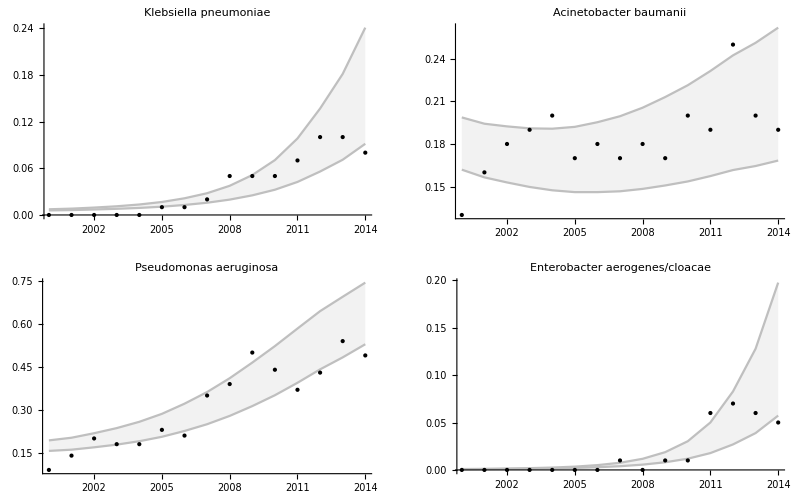
-Graphics-95% confidence interval of model fit and projectionsResistance frequencyYears

```mathematica
plots =Panel[GraphicsGrid[{{Show[plotM[[1]],plotD[[1]],plotS[[1]],plotP[[1]],PlotRange->All],Show[plotM[[2]],plotD[[2]],plotS[[2]],plotP[[2]],PlotRange->All,Axes->True,AxesOrigin->{2000,0.05}]},{Show[plotM[[3]],plotD[[3]],plotS[[3]],plotP[[3]],PlotRange->All],Show[plotM[[4]],plotD[[4]],plotS[[4]],plotP[[4]],PlotRange->All]}},ImageSize->Full],{Style["95% confidence interval of model fit and projections","Panel",32,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",32,Background->White],Style["Years","Panel",32,Background->White]},{{Top,Center},{Left,Center},{Bottom,Center}},Appearance->"Frameless",Background->White]
Export["test.png",plots];
```

# Economic & Health Outcomes

### Mortality

```mathematica
ipneu=5610000; (*pneumonia incidence*)
ipp=cbpp*ipneu; (*pneumonia incidence by pathogen*)

(*carbapenem prescription breakdown for KPC*)
kp={20/105,19/105,29/105,35/105}; (*carbapenem monotherapy, carbapenem combination therapy, sparing mono, sparing combo*)

(*associated mortality rates*)
rkpm={0.467,0.278,0.467,0.304}; (*carbapenem monotherapy, carbapenem combination therapy, sparing mono, sparing combo*)

(*susceptible mortality rates dummy variables*)
skpm={0.234,0.234,0.234,0.234};
```

```mathematica
(*kp # of deaths*)
kpdeath[r_]:=(Total[kp*rkpm]*r + Total[kp*skpm]*(1-r))*ipp[[1]];
Apply[kpdeath,{y[[1]]}]-Apply[kpdeath,{z[[1]]}]
```

Part::partd: Part specification y⟦1⟧ is longer than depth of object.

-321161.+885789. (0.229543 (1-y⟦1⟧)+0.369571 y⟦1⟧)

### Length of Stay

```mathematica
(*Length of stay*)
rlos=5; (*resistant*)
slos=2; (*sensitive*)
wardcost=2877;  (*general ward cost/day*)
```

```mathematica
(*kp general ward costs*)
kplos[r_]:=ipp[[1]]*wardcost*((rlos*((r*(kp[[1]]+kp[[2]]))+(1-r)*(kp[[3]]+kp[[4]])))+(slos*(r*(kp[[3]]*kp[[4]])+((1-r)*(kp[[1]]+kp[[2]])))));
Apply[kplos,{{z[[1]]}}]
```

{5.42489×10^9}